```mathematica
Clear["Global`*"]
```

```mathematica
logspace[a_,b_,c_]=10^(a + ((Range[c]-1))*(b-a)/(c-1));
```

Range::range: Range specification in Range[c] does not have appropriate bounds.

```mathematica
Range[4]/4 -1
```

{-3/4,-1/2,-1/4,0}

```mathematica
(*Parameters*)
```

```mathematica
mp =1.6726219 * 10^-24g;
G = 6.6743*10^-8cm^3/(g*s^2);
c =2.9979246 * 10^10 cm/s;
mass = 1.989*10^42g;
Rb = 20* G * mass / c^2;
Rg = G * mass / c^2;
β=1;
```

```mathematica
1.989*^3
```

1989.

```mathematica
nth0 =1.23*10^4*cm^-3;
nth[r_]=nth0*(r*Rg/Rb)^(-.7);
B[r_]=Sqrt[nth[r]8*Pi*mp*c^2/(β*6r)];
```

```mathematica
start = Log[10,2];
end = 3;
total = 100;
data =Thread[{logspace[start,end,total],B[logspace[start,end,total]]/.{cm->1,s->1,g->1} }] ;
```

```mathematica
p1 =ListLogLogPlot[data, PlotStyle->Red];
```

```mathematica
Bsimple= A1*(r*Rg/Rb)^A2;
{A1Fit,A2Fit}=FindFit[data, Bsimple, {A1, A2}, r]
```

{A1→1.96789,A2→-0.85}

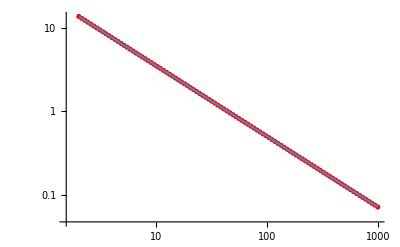

```mathematica
A1f =A1Fit[[2]];
A2f = A2Fit[[2]];
p2 = LogLogPlot[Bsimple/.{A1->A1f,A2->A2f}, {r,2,1000}];
Show[p1,p2]
```